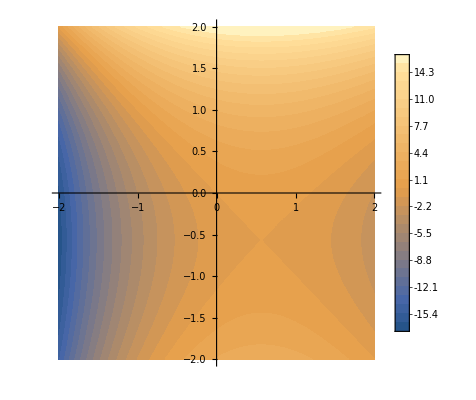

```mathematica
ContourPlot[y^2-x^2+2E^y-2E^(-x),{x,-2,2},{y,-2,2},Axes->True,ContourStyle->None,PlotLegends->Automatic,Frame->False,Contours->30]
```

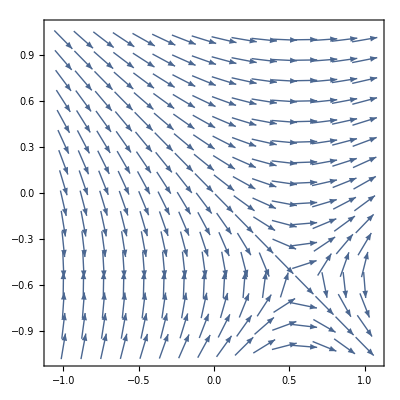

```mathematica
VectorPlot[{Abs[x]/Sqrt[x^2+(x*(x-E^(-x))/(y+E^y))^2],Abs[x]*(x-E^(-x))/(y+E^y)/Sqrt[x^2+(x*(x-E^(-x))/(y+E^y))^2]},{x,-1,1},{y,-1,1},VectorScale->Small,VectorPoints->16]
```